```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/Users/ethanspangler/StabilityProject

```mathematica
"/Users/ethanspangler/StabilityProject"
```

/Users/ethanspangler/StabilityProject

Plots of Freedonia, Merika, and Kleptopia for low initial dissent.

```mathematica
Freedonia =Import["dataFreedonia.mx"] // Dataset;
Merika =Import["dataMerika.mx"] // Dataset;
Kleptopia=Import["dataKleptopia.mx"]//Dataset;
Cathay=Import["dataCathay.mx"]//Dataset;
Rentistan=Import["dataRentistan.mx"]//Dataset;
Develpolus=Import["dataDevelpolus.mx"]//Dataset;
Bellicostia=Import["dataBellicostia.mx"]//Dataset;
Hippieberg=Import["dataHippieberg.mx"]//Dataset;
```

New lines to convert Scientific form to plotable form:

```mathematica
Freedonia = Freedonia/.ScientificForm[n_,rest___]->n;
Merika = Merika/.ScientificForm[n_,rest___]->n;
Kleptopia = Kleptopia/.ScientificForm[n_,rest___]->n;
Cathay= Cathay/.ScientificForm[n_,rest___]->n;
Rentistan= Rentistan/.ScientificForm[n_,rest___]->n;
Develpolus= Develpolus/.ScientificForm[n_,rest___]->n;
Bellicostia= Bellicostia/.ScientificForm[n_,rest___]->n;
Hippieberg= Hippieberg/.ScientificForm[n_,rest___]->n;
```

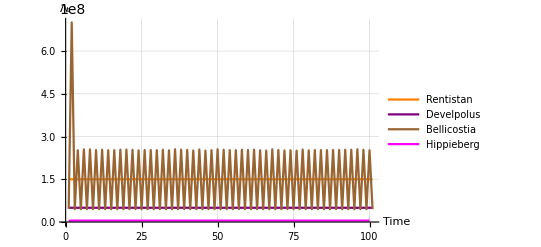

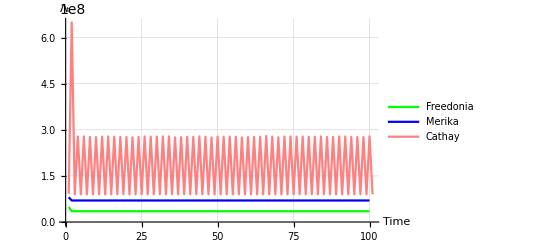

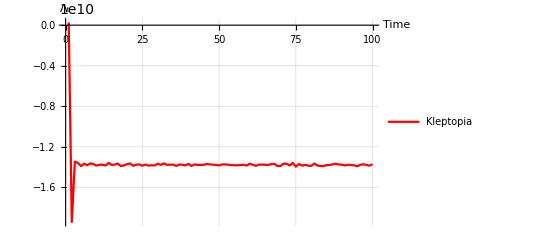

```mathematica
ListLinePlot[{Freedonia[All,3]//Normal,Merika[All,3]//Normal,
Cathay[All,3]//Normal(*,
Rentistan[All,3]//Normal,
Develpolus[All,3] //Normal,
Bellicostia[All,3]//Normal,
Hippieberg[All,3]//Normal*)},PlotLegends->{"Freedonia","Merika","Cathay"(*,"Rentistan","Develpolus","Bellicostia","Hippieberg"*)},PlotStyle->{Green,Blue,Pink(*,Orange,Purple,Magenta,Brown*)},GridLines->Automatic,
(*PlotLabel->Style["Stability with low initial dissent", FontSize->12],*)
PlotRange->Full,AxesLabel->{"Time","Λ_t"}]
ListLinePlot[{(*Freedonia[All,3]//Normal,Merika[All,3]//Normal,
Cathay[All,3]//Normal,*)
Rentistan[All,3]//Normal,
Develpolus[All,3] //Normal,
Bellicostia[All,3]//Normal,
Hippieberg[All,3]//Normal},PlotLegends->{(*"Freedonia","Merika","Cathay",*)"Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{(*Green,Blue,Pink,*)Orange,Purple,Brown, Magenta},GridLines->Automatic,
(*PlotLabel->Style["Stability with low initial dissent", FontSize->12],*)
PlotRange->Full,AxesLabel->{"Time","Λ_t"}]
ListLinePlot[{Kleptopia[All,3]//Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},GridLines->Automatic,
(*PlotLabel->Style["Stability with low initial dissent", FontSize->12],*)
PlotRange->Full,AxesLabel->{"Time","Λ_t"}]
```

Plotting of Initial High Dissent

```mathematica
FreedoniaHD =Import["dataFreedoniaHD.mx"] // Dataset;
MerikaHD =Import["dataMerikaHD.mx"] // Dataset;
KleptopiaHD=Import["dataKleptopiaHD.mx"]//Dataset;
CathayHD=Import["dataCathayHD.mx"]//Dataset;
RentistanHD=Import["dataRentistanHD.mx"]//Dataset;
DevelpolusHD=Import["dataDevelpolusHD.mx"]//Dataset;
BellicostiaHD=Import["dataBellicostiaHD.mx"]//Dataset;
HippiebergHD=Import["dataHippiebergHD.mx"]//Dataset;

FreedoniaHD = FreedoniaHD/.ScientificForm[n_,rest___]->n;
MerikaHD = MerikaHD/.ScientificForm[n_,rest___]->n;
KleptopiaHD = KleptopiaHD/.ScientificForm[n_,rest___]->n;
CathayHD= CathayHD/.ScientificForm[n_,rest___]->n;
RentistanHD= RentistanHD/.ScientificForm[n_,rest___]->n;
DevelpolusHD= DevelpolusHD/.ScientificForm[n_,rest___]->n;
BellicostiaHD= BellicostiaHD/.ScientificForm[n_,rest___]->n;
HippiebergHD= HippiebergHD/.ScientificForm[n_,rest___]->n;
```

```mathematica
ListLinePlot[{FreedoniaHD[All,3]//Normal,MerikaHD[All,3]//Normal(*,Kleptopia[All,3] //Normal*) ,
CathayHD[All,3]//Normal(*,
RentistanRSHOCK[All,3]//Normal,
DevelpolusRSHOCK[All,3] //Normal,
BellicostiaRSHOCK[All,3]//Normal,
HippiebergRSHOCK[All,3]//Normal*)},PlotLegends->{"Freedonia","Merika",(*"Kleptopia",*)"Cathay"},PlotStyle->{Green,Blue(*,Red*),Pink(*,Orange,Purple,Brown, Magenta*)},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}, GridLines->Automatic]
ListLinePlot[{(*FreedoniaRSHOCK[All,3]//Normal,MerikaRSHOCK[All,3]//Normal,KleptopiaRSHOCK[All,3] //Normal ,
CathayRSHOCK[All,3]//Normal,*)
RentistanHD[All,3]//Normal,
DevelpolusHD[All,3] //Normal,
BellicostiaHD[All,3]//Normal,
HippiebergHD[All,3]//Normal},PlotLegends->{(*"Freedonia","Merika","Kleptopia","Cathay",*)"Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{(*Green,Blue,Red,Pink,*)Orange,Purple,Brown, Magenta},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{KleptopiaHD[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
```

Initial Plotting with a R shock,

```mathematica
FreedoniaRSHOCK =Import["dataFreedoniaRSHOCK.mx"] // Dataset;
MerikaRSHOCK =Import["dataMerikaRSHOCK.mx"] // Dataset;
KleptopiaRSHOCK=Import["dataKleptopiaRSHOCK.mx"]//Dataset;
CathayRSHOCK=Import["dataCathayRSHOCK.mx"]//Dataset;
RentistanRSHOCK=Import["dataRentistanRSHOCK.mx"]//Dataset;
DevelpolusRSHOCK=Import["dataDevelpolusRSHOCK.mx"]//Dataset;
BellicostiaRSHOCK=Import["dataBellicostiaRSHOCK.mx"]//Dataset;
HippiebergRSHOCK=Import["dataHippiebergRSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaRSHOCK = FreedoniaRSHOCK/.ScientificForm[n_,rest___]->n
MerikaRSHOCK = MerikaRSHOCK/.ScientificForm[n_,rest___]->n
KleptopiaRSHOCK = KleptopiaRSHOCK/.ScientificForm[n_,rest___]->n
CathayRSHOCK= CathayRSHOCK/.ScientificForm[n_,rest___]->n
RentistanRSHOCK= RentistanRSHOCK/.ScientificForm[n_,rest___]->n
DevelpolusRSHOCK= DevelpolusRSHOCK/.ScientificForm[n_,rest___]->n
BellicostiaRSHOCK= BellicostiaRSHOCK/.ScientificForm[n_,rest___]->n
HippiebergRSHOCK= HippiebergRSHOCK/.ScientificForm[n_,rest___]->n
```

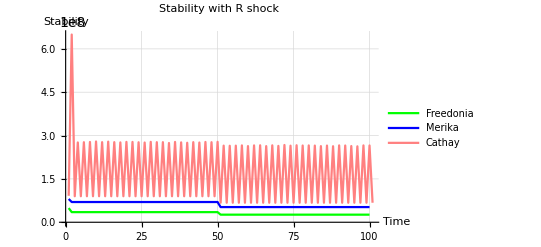

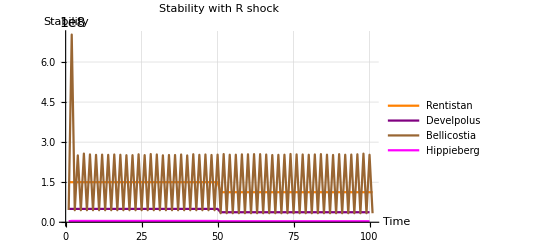

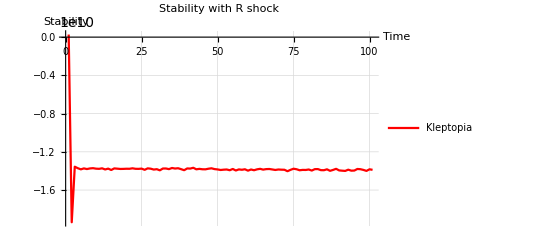

```mathematica
ListLinePlot[{FreedoniaRSHOCK[All,3]//Normal,MerikaRSHOCK[All,3]//Normal(*,KleptopiaRSHOCK[All,3] //Normal*) ,
CathayRSHOCK[All,3]//Normal(*,
RentistanRSHOCK[All,3]//Normal,
DevelpolusRSHOCK[All,3] //Normal,
BellicostiaRSHOCK[All,3]//Normal,
HippiebergRSHOCK[All,3]//Normal*)},PlotLegends->{"Freedonia","Merika",(*"Kleptopia",*)"Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue(*,Red*),Pink(*,Orange,Purple,Brown, Magenta*)},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}, GridLines->Automatic]
ListLinePlot[{(*FreedoniaRSHOCK[All,3]//Normal,MerikaRSHOCK[All,3]//Normal,KleptopiaRSHOCK[All,3] //Normal ,
CathayRSHOCK[All,3]//Normal,*)
RentistanRSHOCK[All,3]//Normal,
DevelpolusRSHOCK[All,3] //Normal,
BellicostiaRSHOCK[All,3]//Normal,
HippiebergRSHOCK[All,3]//Normal},PlotLegends->{(*"Freedonia","Merika","Kleptopia","Cathay",*)"Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{(*Green,Blue,Red,Pink,*)Orange,Purple,Brown, Magenta},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{KleptopiaRSHOCK[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},
PlotLabel->Style["Stability with R shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
```

ϕ shock plotting,

```mathematica
FreedoniaPhiSHOCK =Import["dataFreedoniaPhiSHOCK.mx"] // Dataset;
MerikaPhiSHOCK =Import["dataMerikaPhiSHOCK.mx"] // Dataset;
KleptopiaPhiSHOCK=Import["dataKleptopiaPhiSHOCK.mx"]//Dataset;
CathayPhiSHOCK=Import["dataCathayPhiSHOCK.mx"]//Dataset;
RentistanPhiSHOCK=Import["dataRentistanPhiSHOCK.mx"]//Dataset;
DevelpolusPhiSHOCK=Import["dataDevelpolusPhiSHOCK.mx"]//Dataset;
BellicostiaPhiSHOCK=Import["dataBellicostiaPhiSHOCK.mx"]//Dataset;
HippiebergPhiSHOCK=Import["dataHippiebergPhiSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaPhiSHOCK = FreedoniaPhiSHOCK/.ScientificForm[n_,rest___]->n;
MerikaPhiSHOCK = MerikaPhiSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaPhiSHOCK = KleptopiaPhiSHOCK/.ScientificForm[n_,rest___]->n;
CathayPhiSHOCK= CathayPhiSHOCK/.ScientificForm[n_,rest___]->n;
RentistanPhiSHOCK= RentistanPhiSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusPhiSHOCK= DevelpolusPhiSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaPhiSHOCK= BellicostiaPhiSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergPhiSHOCK= HippiebergPhiSHOCK/.ScientificForm[n_,rest___]->n;
```

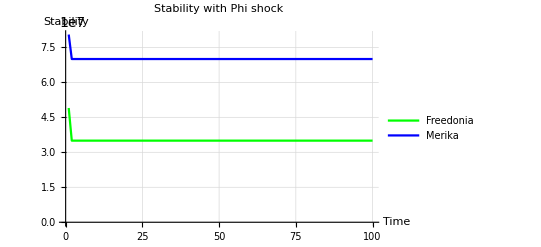

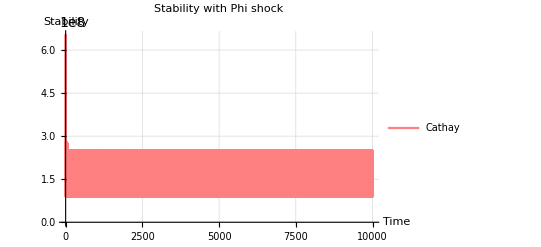

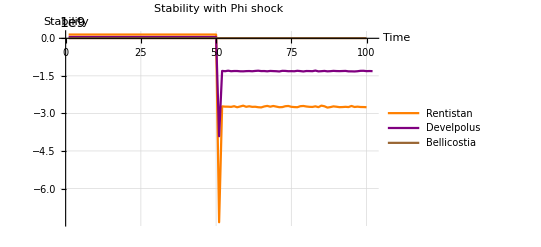

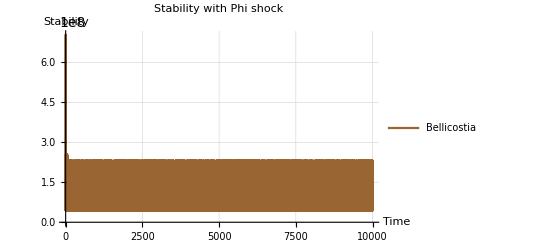

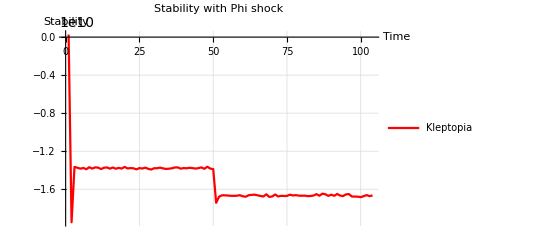

```mathematica
ListLinePlot[{FreedoniaPhiSHOCK[All,3]//Normal,
MerikaPhiSHOCK[All,3]//Normal
(*CathayPhiSHOCK[All,3]//Normal*)},
PlotLegends->{"Freedonia","Merika","Cathay"},
PlotStyle->{Green,Blue,Pink},
PlotLabel->Style["Stability with Phi shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}, GridLines->Automatic]
ListLinePlot[{CathayPhiSHOCK[All,3] //Normal },PlotLegends->{"Cathay"},PlotStyle->{Pink},
PlotLabel->Style["Stability with Phi shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{
RentistanPhiSHOCK[All,3]//Normal,
DevelpolusPhiSHOCK[All,3] //Normal,
(*BellicostiaPhiSHOCK[All,3]//Normal,*)
HippiebergPhiSHOCK[All,3]//Normal},
PlotLegends->{"Rentistan","Develpolus","Bellicostia","Hippieberg"},
PlotStyle->{Orange,Purple,Brown, Magenta},
PlotLabel->Style["Stability with Phi shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{BellicostiaPhiSHOCK[All,3] //Normal },PlotLegends->{"Bellicostia"},PlotStyle->{Brown},
PlotLabel->Style["Stability with Phi shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]

ListLinePlot[{KleptopiaPhiSHOCK[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},
PlotLabel->Style["Stability with Phi shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
```

Ω shock plotting,

```mathematica
FreedoniaOSHOCK =Import["dataFreedoniaOSHOCK.mx"] // Dataset;
MerikaOSHOCK =Import["dataMerikaOSHOCK.mx"] // Dataset;
KleptopiaOSHOCK=Import["dataKleptopiaOSHOCK.mx"]//Dataset;
CathayOSHOCK=Import["dataCathayOSHOCK.mx"]//Dataset;
RentistanOSHOCK=Import["dataRentistanOSHOCK.mx"]//Dataset;
DevelpolusOSHOCK=Import["dataDevelpolusOSHOCK.mx"]//Dataset;
BellicostiaOSHOCK=Import["dataBellicostiaOSHOCK.mx"]//Dataset;
HippiebergOSHOCK=Import["dataHippiebergOSHOCK.mx"]//Dataset;
```

Import::nffil: File not found during Import.

Dataset`ExtractRawData::dataextr: Data extraction failed.

```mathematica
FreedoniaOSHOCK = FreedoniaOSHOCK/.ScientificForm[n_,rest___]->n;
MerikaOSHOCK = MerikaOSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaOSHOCK = KleptopiaOSHOCK/.ScientificForm[n_,rest___]->n;
CathayOSHOCK= CathayOSHOCK/.ScientificForm[n_,rest___]->n;
RentistanOSHOCK= RentistanOSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusOSHOCK= DevelpolusOSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaOSHOCK= BellicostiaOSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergOSHOCK= HippiebergOSHOCK/.ScientificForm[n_,rest___]->n;
```

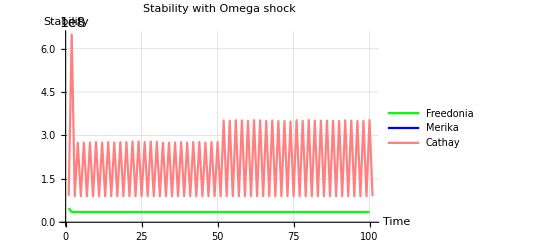

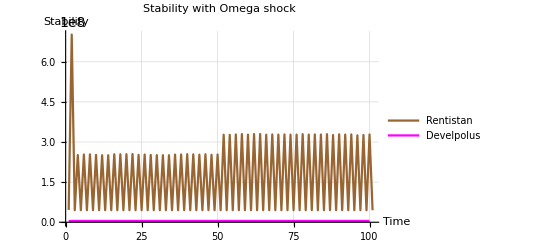

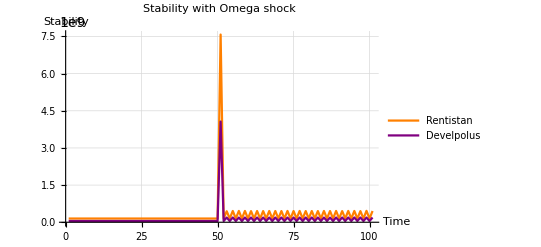

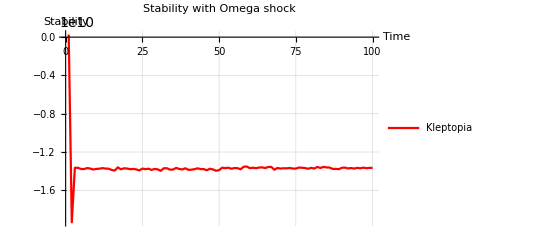

```mathematica
ListLinePlot[{FreedoniaOSHOCK[All,3]//Normal,
MerikaOSHOCK[All,3]//Normal,
CathayOSHOCK[All,3]//Normal},
PlotLegends->{"Freedonia","Merika","Cathay"},
PlotStyle->{Green,Blue,Pink},
PlotLabel->Style["Stability with Omega shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}, GridLines->Automatic]
ListLinePlot[{(*
RentistanOSHOCK[All,3]//Normal,
DevelpolusOSHOCK[All,3] //Normal,*)
BellicostiaOSHOCK[All,3]//Normal,
HippiebergOSHOCK[All,3]//Normal},
PlotLegends->{"Rentistan","Develpolus","Bellicostia","Hippieberg"},
PlotStyle->{(*Orange,Purple,*)Brown, Magenta},
PlotLabel->Style["Stability with Omega shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{
RentistanOSHOCK[All,3]//Normal,
DevelpolusOSHOCK[All,3] //Normal
(*BellicostiaOSHOCK[All,3]//Normal,
HippiebergOSHOCK[All,3]//Normal*)},
PlotLegends->{"Rentistan","Develpolus"(*,"Bellicostia","Hippieberg"*)},
PlotStyle->{Orange,Purple(*,Brown, Magenta*)},
PlotLabel->Style["Stability with Omega shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{KleptopiaOSHOCK[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},
PlotLabel->Style["Stability with Omega shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
```

E shock plotting,

```mathematica
FreedoniaEtSHOCK =Import["dataFreedoniaEtSHOCK.mx"] // Dataset;
MerikaEtSHOCK =Import["dataMerikaEtSHOCK.mx"] // Dataset;
KleptopiaEtSHOCK=Import["dataKleptopiaEtSHOCK.mx"]//Dataset;
CathayEtSHOCK=Import["dataCathayEtSHOCK.mx"]//Dataset;
RentistanEtSHOCK=Import["dataRentistanEtSHOCK.mx"]//Dataset;
DevelpolusEtSHOCK=Import["dataDevelpolusEtSHOCK.mx"]//Dataset;
BellicostiaEtSHOCK=Import["dataBellicostiaEtSHOCK.mx"]//Dataset;
HippiebergEtSHOCK=Import["dataHippiebergEtSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaEtSHOCK = FreedoniaEtSHOCK/.ScientificForm[n_,rest___]->n;
MerikaEtSHOCK = MerikaEtSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaEtSHOCK = KleptopiaEtSHOCK/.ScientificForm[n_,rest___]->n;
CathayEtSHOCK= CathayEtSHOCK/.ScientificForm[n_,rest___]->n;
RentistanEtSHOCK= RentistanEtSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusEtSHOCK= DevelpolusEtSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaEtSHOCK= BellicostiaEtSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergEtSHOCK= HippiebergEtSHOCK/.ScientificForm[n_,rest___]->n;
```

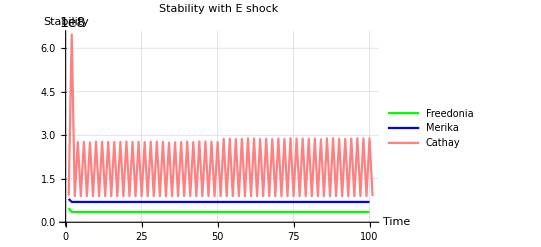

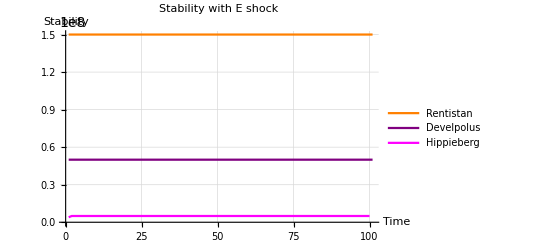

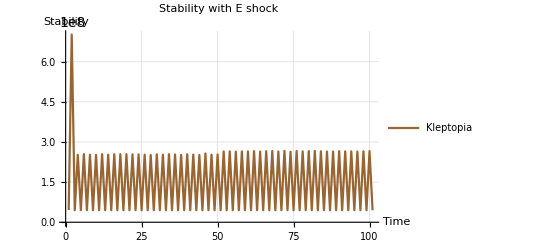

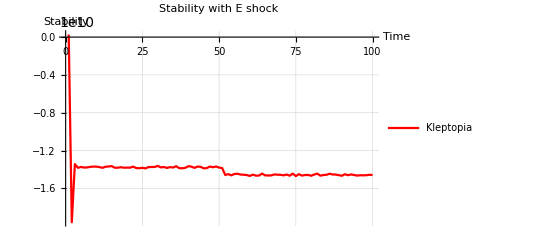

```mathematica
ListLinePlot[{FreedoniaEtSHOCK[All,3]//Normal,
MerikaEtSHOCK[All,3]//Normal,
CathayEtSHOCK[All,3]//Normal},
PlotLegends->{"Freedonia","Merika","Cathay"},
PlotStyle->{Green,Blue,Pink},
PlotLabel->Style["Stability with E shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}, GridLines->Automatic]
ListLinePlot[{
RentistanEtSHOCK[All,3]//Normal,
DevelpolusEtSHOCK[All,3] //Normal,
(*BellicostiaEtSHOCK[All,3]//Normal,*)
HippiebergEtSHOCK[All,3]//Normal},
PlotLegends->{"Rentistan","Develpolus","Hippieberg"},
PlotStyle->{Orange,Purple, Magenta},
PlotLabel->Style["Stability with E shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{BellicostiaEtSHOCK[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Brown},
PlotLabel->Style["Stability with E shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{KleptopiaEtSHOCK[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},
PlotLabel->Style["Stability with E shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
```

Policing (Es) shock plotting,

```mathematica
FreedoniaEsSHOCK =Import["dataFreedoniaEsSHOCK.mx"] // Dataset;
MerikaEsSHOCK =Import["dataMerikaEsSHOCK.mx"] // Dataset;
KleptopiaEsSHOCK=Import["dataKleptopiaEsSHOCK.mx"]//Dataset;
CathayEsSHOCK=Import["dataCathayEsSHOCK.mx"]//Dataset;
RentistanEsSHOCK=Import["dataRentistanEsSHOCK.mx"]//Dataset;
DevelpolusEsSHOCK=Import["dataDevelpolusEsSHOCK.mx"]//Dataset;
BellicostiaEsSHOCK=Import["dataBellicostiaEsSHOCK.mx"]//Dataset;
HippiebergEsSHOCK=Import["dataHippiebergEsSHOCK.mx"]//Dataset;
```

Import::nffil: File not found during Import.

Dataset`ExtractRawData::dataextr: Data extraction failed.

Import::nffil: File not found during Import.

Dataset`ExtractRawData::dataextr: Data extraction failed.

```mathematica
FreedoniaEsSHOCK = FreedoniaEsSHOCK/.ScientificForm[n_,rest___]->n;
MerikaEsSHOCK = MerikaEsSHOCK/.ScientificForm[n_,rest___]->n;
KleptopiaEsSHOCK = KleptopiaEsSHOCK/.ScientificForm[n_,rest___]->n;
CathayEsSHOCK= CathayEsSHOCK/.ScientificForm[n_,rest___]->n;
RentistanEsSHOCK= RentistanEsSHOCK/.ScientificForm[n_,rest___]->n;
DevelpolusEsSHOCK= DevelpolusEsSHOCK/.ScientificForm[n_,rest___]->n;
BellicostiaEsSHOCK= BellicostiaEsSHOCK/.ScientificForm[n_,rest___]->n;
HippiebergEsSHOCK= HippiebergEsSHOCK/.ScientificForm[n_,rest___]->n;
```

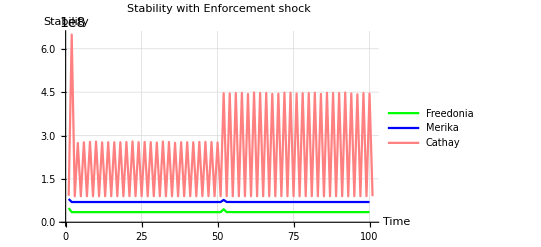

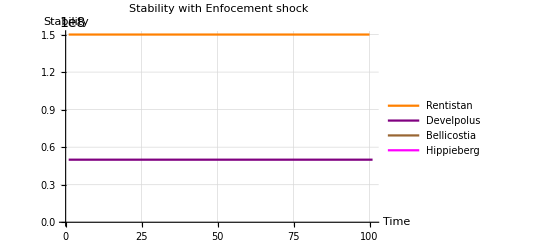

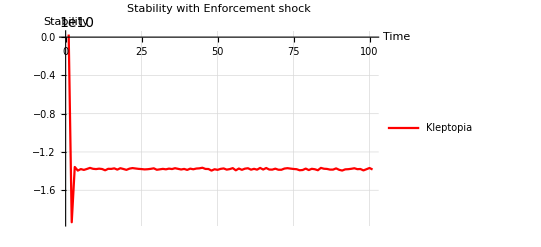

```mathematica
ListLinePlot[{FreedoniaEsSHOCK[All,3]//Normal,
MerikaEsSHOCK[All,3]//Normal,
CathayEsSHOCK[All,3]//Normal},
PlotLegends->{"Freedonia","Merika","Cathay"},
PlotStyle->{Green,Blue,Pink},
PlotLabel->Style["Stability with Enforcement shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}, GridLines->Automatic]
ListLinePlot[{
RentistanEsSHOCK[All,3]//Normal,
DevelpolusEsSHOCK[All,3] //Normal,
BellicostiaEsSHOCK[All,3]//Normal,
HippiebergEsSHOCK[All,3]//Normal},
PlotLegends->{"Rentistan","Develpolus","Bellicostia","Hippieberg"},
PlotStyle->{Orange,Purple,Brown, Magenta},
PlotLabel->Style["Stability with Enfocement shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
ListLinePlot[{KleptopiaEsSHOCK[All,3] //Normal },PlotLegends->{"Kleptopia"},PlotStyle->{Red},
PlotLabel->Style["Stability with Enforcement shock", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"},GridLines->Automatic]
```